```mathematica
img=-Graphics-;
```

```mathematica
ImageDimensions[img]
```

```mathematica
{1080/40,1920/40}//N
```

{27.,48.}

```mathematica
ImagePartition[img,40]⟦2,1⟧
```

-Graphics-

```mathematica
imgData=ImageData[img];
```

```mathematica
First[Position[imgData⟦All,1⟧,{1.,1.,1.}]]
```

{217}

```mathematica
plotData=Table[{i,Total[imgData⟦All,1⟧⟦i⟧]},{i,1920}];
```

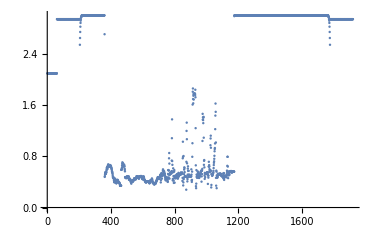

```mathematica
ListPlot[plotData]
```

```mathematica
graphPlot[img_]:=Module[{imgData,plotData},
imgData=ImageData[img];
plotData=Table[{i,Total[imgData⟦All,500⟧⟦i⟧]},{i,1920}];
ListPlot[plotData]
];
```

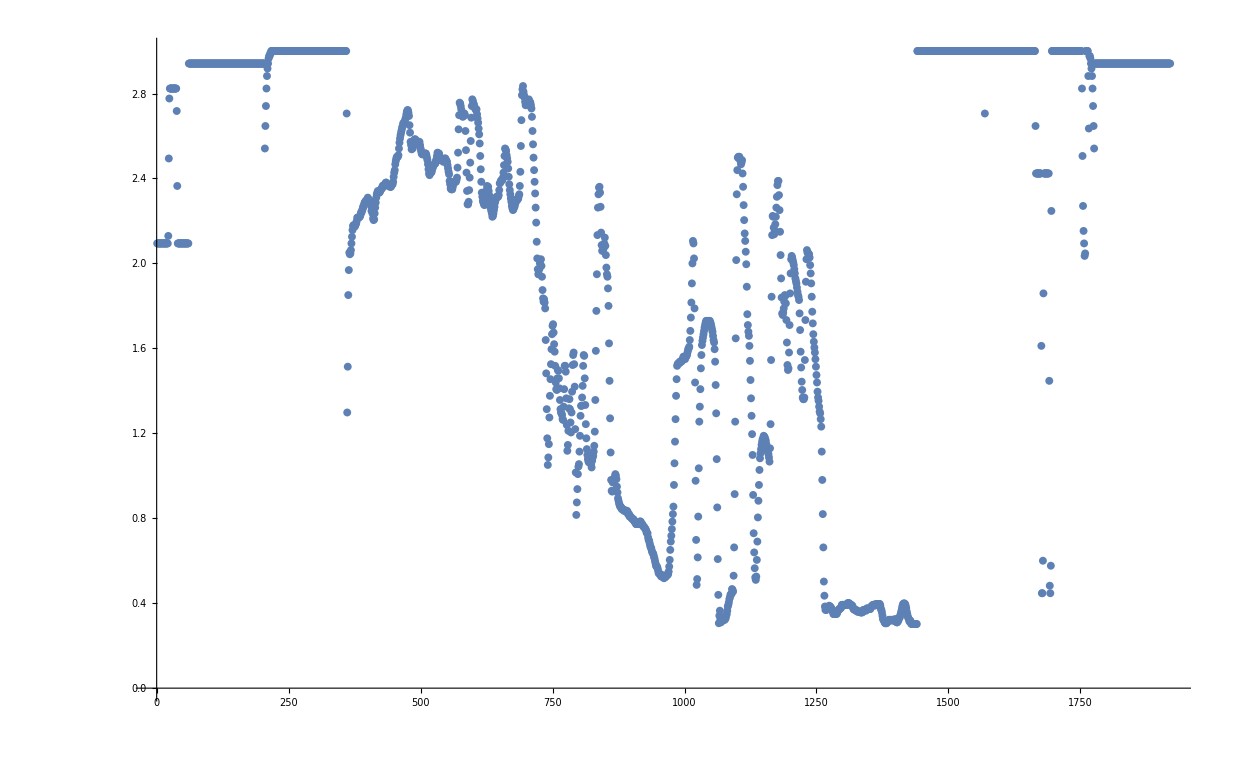

```mathematica
graphPlot[-Graphics-]
```

```mathematica
i=1;
While[
imgData⟦i,1⟧=={1.,1.,1.}||
imgData⟦i+1,1⟧=={1.,1.,1.}||
imgData⟦i+2,1⟧=={1.,1.,1.}||
imgData⟦i+3,1⟧=={1.,1.,1.},
Print[i];
i++
]
```

```mathematica
{imgData⟦1,1⟧,imgData⟦2,1⟧,imgData⟦3,1⟧,imgData⟦4,1⟧}
```

{{0.698039,0.698039,0.698039},{0.698039,0.698039,0.698039},{0.698039,0.698039,0.698039},{0.698039,0.698039,0.698039}}